## Constants

```mathematica
Tcmb=2.7255;
c=299792.458;
cH0=2997.92458;
KtoeV=8.621738*10^-5;
cmtoeV=1/8065.544005;
Neff=3.044;
Ωγh2=Pi^2/30  gγ T^4/ρcr…over…h2/.T->Tcmb K/.gγ->2/.GeV->10^9 eV/.K->KtoeV eV;
ρcr…over…h2=8.098*10^-11 eV^4;
Ωγ[h_]:=Ωγh2/h^2;
Ων[h_,Neff_]:=Neff*7/8 (4/11)^(4/3) Ωγ[h]
Ωr[h_,Neff_]:=Ωγ[h]+Ων[h,Neff];
```

```mathematica
w[a_,w0_,wa_]:=w0+wa(1-a)
f[a_,w0_,wa_]:=a^(-3 (1+w0+wa)) E^(1/2 (-1+a) (6 wa))
(*Other Parametrizations: 
LOG: w=w0+wa*Log[1+(1/a-1)], f=(1+(1/a-1))^(3+3 w0+3/2 wa Log[1+(1/a-1)]) 
BA: w=w0+wa*((1/a-1)*(1+(1/a-1))/(1+(1/a-1)^2)), f=(1+(1/a-1))^(3+3 w0) (1+(1/a-1)^2)^(3 wa/2)
 JBP:w=w0+wa*((1/a-1)/(1+(1/a-1))^2), f=E^((3 wa (1/a-1)^2)/(2 (1+(1/a-1))^2)) (1+(1/a-1))^(3+3 w0)*)


H[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=100h Sqrt[om a^-3+Ωr[h,Neff] a^-4+(1-om-Ωr[h,Neff])f[a,w0,wa]]

(* Densities *)
ΩDE[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=((1-om-Ωr[h,Neff])f[a,w0,wa])/(H[a,om,w0,wa,h]/(100h))^2
Ωrel[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=(Ωr[h,Neff]a^-4)/(H[a,om,w0,wa,h]/(100h))^2
Ωm[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=(om a^-3)/(H[a,om,w0,wa,h]/(100h))^2
cs[a_?NumberQ,obh2_?NumberQ]:=c Sqrt[1/(3(1+3/4 obh2/Ωγh2 a))]


(* Redshift at decoupling Eq. (A4) from 2106.00428 *)
zcmb…GA[ωm_?NumberQ,ωb_?NumberQ]:=(391.672 ωm^(−0.372296)+937.422 ωb^(−0.97966))/(ωm^(−0.0192951) ωb^(−0.93681))+ωm^(−0.731631)
(* Redshift at decoupling Eq. (A2) from 2106.00428 *)
zdrag…GA[ωm_?NumberQ,ωb_?NumberQ]:=1/ωm^0.714129 (1+428.169 ωb^0.256459 ωm^0.616388+925.56 ωm^0.751615)
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=(DLsol[om,w0,wa,h]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(H[1/(1+zz),om,w0,wa,h]/(100h)),dL[0]==0},dL,{zz,0,1500},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=(c/(100h) dL[z]/.DLsol[om,w0,wa,h])[[1]]//Chop
DA[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=1/(1+z)^2 DL[z,om,w0,wa,h]

(* Comoving sound horizon at drag redshift *)
rs…num[ze_,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=NIntegrate[cs[A,obh2]/(A^2H[A,om,w0,wa,h]),{A,0,1/(1+ze[om h^2,obh2])}]
rsd…GA[ωm_,ωb_]:=Module[{a1=0.00257366,a2=0.05032,a3=0.013,a4=0.7720642,a5=0.24346362,a6=0.00641072,a7=0.5350899,a8=32.7525,a9=0.315473},1/(a1 ωb^a2+a3 ωb^a4 ωm^a5+a6 ωm^a7)-a8/ωm^a9]
(* Sound horizon from 2212.04522 *)
rsd…HGM[ωm_,ωb_]:=147.05 (ωm/0.1432)^-0.23 (3.044/3.04)^-0.1 (ωb/0.02236)^-0.13
(* Dilation scale *)
Dv[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=(((1+z)DA[z,om,w0,wa,h] )^2  ((c*z)/H[1/(1+z),om,w0,wa,h]))^(1/3)
(* BAO Subscript[d, z] ratio *)
dz[z_?NumberQ,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=rs…num[zdrag…GA,om,obh2,w0,wa,h]/Dv[z,om,w0,wa,h]
(* DH "distance" *)
DH[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=c/H[1/(1+z),om,w0,wa,h]
(* Scaled distance at recombination *)
R[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=Sqrt[om (100h)^2]DA[zcmb…GA[om h^2,obh2],om,w0,wa,h](1+zcmb…GA[om h^2,obh2])/c
(* Angular scale of sound horizon at recombination *)
la[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=π (DA[zcmb…GA[om h^2,obh2],om,w0,wa,h](1+zcmb…GA[om h^2,obh2]))/(rs…num[zcmb…GA,om,obh2,w0,wa,h])

(* DM "distance" *)
DM[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=(1+z)DA[z,om,w0,wa,h]

(* DM "distance" ratio over rs(zd) *)
DM…over…rs[z_?NumberQ,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=((1+z)DA[z,om,w0,wa,h])/rs…num[zdrag…GA,om,obh2,w0,wa,h]

DM…over…DH[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=DM[z,om,w0,wa,h]/DH[z,om,w0,wa,h]
```

## DESI DR2 DATA ( see Table IV, https://arxiv.org/pdf/2503.14738 , on page 14)

```mathematica
BGS…σ=0.075;
LRG1…σ={0.099,0.017,0.05};
LRG2…σ={0.110,0.021,−0.018};
LRG3…ELG1…σ={0.091,0.019,0.056};
ELG2…σ={0.174,0.045,0.202};
QSO…σ={0.398,0.136,0.044};
Lya…σ={0.256,0.097,0.574};
(* The values *)
```

```mathematica
data…BAO={{0.295,7.942},{0.510,12.720},{0.510,0.622},{0.706,16.048},{0.706,0.892},{0.934,19.721},{0.934,1.223},{1.321,24.256},{1.321,1.948},{1.484,26.059},{1.484,2.386},{2.330,31.267},{2.330,4.518}};
make…cij[vec_List]:={{vec[[1]]^2,vec[[1]] vec[[2]]vec[[3]]},{vec[[1]] vec[[2]]vec[[3]],vec[[2]]^2}}
make…cij[vec_]:=vec^2
Cij…DESI=ConstantArray[0,{Length[data…BAO],Length[data…BAO]}];
Cij…DESI[[1,1]]=make…cij@BGS…σ;
Cij…DESI[[{2,3},{2,3}]]=make…cij@LRG1…σ;
Cij…DESI[[{4,5},{4,5}]]=make…cij@LRG2…σ;
Cij…DESI[[{6,7},{6,7}]]=make…cij@LRG3…ELG1…σ;
Cij…DESI[[{8,9},{8,9}]]=make…cij@ELG2…σ;
Cij…DESI[[{10,11},{10,11}]]=make…cij@QSO…σ;
Cij…DESI[[{12,13},{12,13}]]=make…cij@Lya…σ;
Fij…DESI=Inverse[Cij…DESI];

chi2…BBN…DESI[obh2_?NumberQ]:=((obh2-0.02218)/0.00055)^2


chi2…BAO…DESI…GA[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=Module[{V…data,V…theory,ΔV,rd},rd=rsd…GA[om h^2,obh2];
V…theory={Dv[data…BAO[[1,1]],om,w0,wa,h]/rd,Dv[data…BAO[[2,1]],om,w0,wa,h]/rd,DM…over…DH[data…BAO[[3,1]],om,w0,wa,h],Dv[data…BAO[[4,1]],om,w0,wa,h]/rd,DM…over…DH[data…BAO[[5,1]],om,w0,wa,h],Dv[data…BAO[[6,1]],om,w0,wa,h]/rd,DM…over…DH[data…BAO[[7,1]],om,w0,wa,h],Dv[data…BAO[[8,1]],om,w0,wa,h]/rd,DM…over…DH[data…BAO[[9,1]],om,w0,wa,h],Dv[data…BAO[[10,1]],om,w0,wa,h]/rd,DM…over…DH[data…BAO[[11,1]],om,w0,wa,h],Dv[data…BAO[[12,1]],om,w0,wa,h]/rd,DM…over…DH[data…BAO[[13,1]],om,w0,wa,h]};
V…data=data…BAO[[All,2]];
ΔV=V…theory-V…data;
ΔV.Fij…DESI.ΔV]
```

## Growth Data

```mathematica
amin=1/(1+1090);
zCMB=1/amin-1;
muGfull[a_,n_,ga_]:=1.00002+ga (1-a)^n-ga (1-a)^(2n)

f0[z_,w0_,wa_]:=ⅇ^(-(3 wa z)/(1+z)) (1+z)^(3 (1+w0+wa)) (*Update this function accordingly when changing parametrization*)
HoverH0[z_,om_,w0_,wa_]:=Sqrt[om (1+z)^3+(1-om) f0[z,w0,wa]];

dsol1[om_?NumberQ,n_?NumberQ,ga_?NumberQ,w0_,wa_]:=(dsol1[om,n,ga,w0,wa]=Module[{a},NDSolve[{-((3 om d0[a] HoverH0[0,om,w0,wa]^2)/(2 a^5 HoverH0[1/a-1,om,w0,wa]^2))(muGfull[a,n,ga])+d0'[a] (3/a+D[HoverH0[1/a-1,om,w0,wa],a]/HoverH0[1/a-1,om,w0,wa])+d0''[a]==0,d0[amin]==amin,d0'[amin]==1},d0,{a,amin,1}][[1]]])
(* The growth rate and fσ8 *)
Da[a_?NumberQ,om_?NumberQ,n_?NumberQ,ga_?NumberQ,w0_,wa_]:=d0[a]/.dsol1[om,n,ga,w0,wa]
fa[aa_,om_?NumberQ,n_?NumberQ,ga_?NumberQ,w0_,wa_]:=a d0'[a]/d0[a]/.a->aa/.dsol1[om,n,ga,w0,wa]
fσ8[a_?NumberQ,om_?NumberQ,n_?NumberQ,ga_?NumberQ,w0_,wa_,σ8_?NumberQ]:=(σ8 Da[aa,om,n,ga,w0,wa])/Da[1,om,n,ga,w0,wa] fa[aa,om,n,ga,w0,wa]/.aa->a
fσ8z[z_?NumberQ,om_?NumberQ,n_?NumberQ,ga_?NumberQ,w0_,wa_,σ8_?NumberQ]:=(σ8 Da[aa,om,n,ga,w0,wa])/Da[1,om,n,ga,w0,wa] fa[aa,om,n,ga,w0,wa]/.aa->1/(1+z)
```

## Import Growth Data (( see Table A1 on Appendix A of the following article https://arxiv.org/pdf/2507.22780 ) )

```mathematica
datagrowth=Import["data_growth_2025v.txt","Table"];
dataWiggleZ=Import["GrowthData-v\\wigglezdat.txt","Table"];
```

```mathematica
CijWiggleZ=({{0.00640, 0.002570, 0.000000}, {0.00257, 0.003969, 0.002540}, {0.00000, 0.002540, 0.005184}});

invcijwiggle=Inverse[CijWiggleZ];
Cijfs81=DiagonalMatrix[datagrowth[[All,3]]^2];
InvCijfs81=Inverse[Cijfs81];
(* χ^2 correlated term Scalar Tensor Theory *)
vecgr[data_,om_?NumberQ,n_?NumberQ,ga_?NumberQ,w0_,wa_,σ8_?NumberQ]:=Table[data[[i,2]]-fσ8[1/(1+data[[i,1]]),om,n,ga,w0,wa,σ8],{i,1,Length[data]}]
chi2corrunc[data_,om_?NumberQ,n_?NumberQ,ga_?NumberQ,w0_,wa_,σ8_?NumberQ]:=vecgr[data,om,n,ga,w0,wa,σ8].InvCijfs81.vecgr[data,om,n,ga,w0,wa,σ8]
chi2corrwigglez[data_,om_?NumberQ,n_?NumberQ,ga_?NumberQ,w0_,wa_,σ8_?NumberQ]:=vecgr[data,om,n,ga,w0,wa,σ8].invcijwiggle.vecgr[data,om,n,ga,w0,wa,σ8]

chi2growth[om_,n_,ga_,w0_,wa_,σ8_]:=chi2corrunc[datagrowth,om,n,ga,w0,wa,σ8]+chi2corrwigglez[dataWiggleZ,om,n,ga,w0,wa,σ8]
```

## CMB DATA

```mathematica
(* Central values for {R, Subscript[l, a], Subscript[Ω, b] h^2} from Planck 2018 for a flat universe - See Eq. (31) of https://arxiv.org/pdf/1811.07425.pdf on page 7 *)
datacmb={1.74963,301.80845,0.02237};
(* Inverse Covariance Matrix using  for {R, Subscript[l, a], Subscript[Ω, b] h^2} *)
covcmb=10^-8({{1598.9554, 17112.007, −36.311179}, {17112.007, 811208.45, −494.79813}, {-36.311179, -494.79813, 2.1242182}});
invcov=Inverse[covcmb];
(* χ^2 for R *)
vec[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:={R[om,obh2,w0,wa,h]-datacmb[[1]],la[om,obh2,w0,wa,h]-datacmb[[2]],obh2-datacmb[[3]]};
chi2…CMB[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=vec[om,obh2,w0,wa,h] . invcov . vec[om,obh2,w0,wa,h]
```

## Pantheon+ Data

```mathematica
(* Import the full Pantheon data as can be found in https://github.com/Dimitrios1993/Reconstructing-Scalar-Tensor-Theories*)
dataPanth=Import["lcparam_full_long_zhel-pp.txt","Table"];
(* Length of Pantheon data *)
ndatPanth=Length[dataPanth]-1;
(* Import the systematic errors which are in a separate file *)
Dij0=Import["sys_full_long-pp.txt","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
Covsys=Dij;
(* Total Covariance *)
Cijtot=Covsys;
InvCovTotal=Inverse[Cijtot];

(* χ^2 for the Pantheon+ data. Note that to obtain the quasi-degenerate contour for Subscript[σ, 8] and Subscript[g, a], remove the term "-1.465/2Log10[muGfull[1/(1 + dataPanth[[1 + i, 3]]),2,ga]]"  and rerun*)
chi2Panth[M_?NumberQ,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,ga_?NumberQ]:=
Module[{Δm},
Δm=Table[If[dataPanth[[1+i,14]]==1,dataPanth[[1+i,9]]-(M-1.46 5/2 Log10[muGfull[1/(1+dataPanth[[1+i,3]]),2,ga]]) -dataPanth[[1+i,13]],dataPanth[[1+i,9]]-((M-1.46 5/2 Log10[muGfull[1/(1+dataPanth[[1+i,3]]),2,ga]]) +5 Log10[DL[dataPanth[[1+i,3]],om,w0,wa,h]]+25)],{i,1,ndatPanth}];
Δm.InvCovTotal.Δm]
```

## Total χ^2:

```mathematica
(* The total chi^2 for the new data *)
chi2…total[M_?NumberQ,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,ga_?NumberQ,σ8_?NumberQ,h_?NumberQ,n_?NumberQ]:=chi2…CMB[om,obh2,w0,wa,h]+chi2…BAO…DESI…GA[om,obh2,w0,wa,h]+chi2Panth[M,om,obh2,w0,wa,h,ga]+chi2growth[om,n,ga,w0,wa,σ8]
```

```mathematica
NMinimize[{chi2…total[M,om,obh2,w0,wa,ga,σ8,h,2],-19.4<=M<=-19.3,0.28<=om<=0.301,0.02218<=obh2<=0.0223,-1.05<=w0<=-0.85,-0.7<=wa<=-0.1,-0.1<=ga<=0.5,0.75<=σ8<=0.795,0.680<=h<=0.739},{M,om,obh2,w0,wa,ga,σ8,h},Method->"DifferentialEvolution"]
```

{1571.21,{M→-19.3374,om→0.286253,obh2→0.0223,w0→-1.01341,wa→-0.342229,ga→0.322089,σ8→0.780831,h→0.705644}}

```mathematica
fmwc5={1571.2108434858928,{M->-19.33738984974981,om->0.286252567505367,obh2->0.022299999999745683,w0->-1.013406665170472,wa->-0.34222910997496503,ga->0.32208887943795345,σ8->0.7808305901073777,h->0.7056442892036879}}
```

{1571.21,{M→-19.3374,om→0.286253,obh2→0.0223,w0→-1.01341,wa→-0.342229,ga→0.322089,σ8→0.780831,h→0.705644}}

```mathematica
om0=fmwc5[[2,2,2]];
w01=fmwc5[[2,4,2]];
wa1=fmwc5[[2,5,2]];
γ0=fmwc5[[2,6,2]];
sigma8=fmwc5[[2,7,2]];
```

```mathematica
deltachi2[nsig_,m_]:=2 InverseGammaRegularized[m/2,1-Erf[nsig/(√2)]]
```

```mathematica
contlcdm2=ContourPlot[chi2…total[fmwc5[[2,1,2]],om0,fmwc5[[2,3,2]],w01,wa1,ga,s8,fmwc5[[2,8,2]],2],{ga,0.,0.5},{s8,0.7,0.9},Contours->{fmwc5[[1]]+deltachi2[1,2],fmwc5[[1]]+deltachi2[2,2]},ContourShading->{Cyan,RGBColor[0.78,1,0.96], White},ContourStyle->{{Gray,Dashed},{Gray,Dashed}}];
```

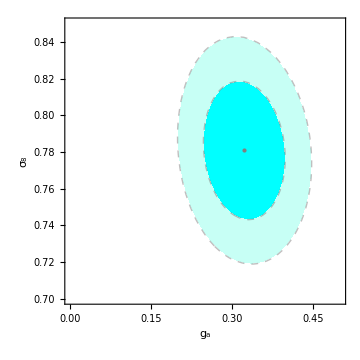

```mathematica
Show[{contlcdm2},Epilog->{{PointSize[Medium],Gray,Point[{γ0,sigma8}]}},FrameLabel->{"g_a","σ_8"},PlotRange->{{-0.,0.5},{0.7,0.85}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Medium]
```

```mathematica
chifun01=ListInterpolation[ParallelTable[chi2…total[M,om,obh2,w0,wa,ga,σ8,h,2],{M,fmwc5[[2,1,2]]-0.01,fmwc5[[2,1,2]]+0.01,0.01},{om,fmwc5[[2,2,2]]-0.01,fmwc5[[2,2,2]]+0.01,0.01},{obh2,fmwc5[[2,3,2]]-0.01,fmwc5[[2,3,2]]+0.01,0.01},{w0,fmwc5[[2,4,2]]-0.01,fmwc5[[2,4,2]]+0.01,0.01},{wa,fmwc5[[2,5,2]]-0.01,fmwc5[[2,5,2]]+0.01,0.01},{ga,fmwc5[[2,6,2]]-0.01,fmwc5[[2,6,2]]+0.01,0.01},{σ8,fmwc5[[2,7,2]]-0.01,fmwc5[[2,7,2]]+0.01,0.01},{h,fmwc5[[2,8,2]]-0.01,fmwc5[[2,8,2]]+0.01,0.01},DistributedContexts->Automatic],{{fmwc5[[2,1,2]]-0.01,fmwc5[[2,1,2]]+0.01},{fmwc5[[2,2,2]]-0.01,fmwc5[[2,2,2]]+0.01},{fmwc5[[2,3,2]]-0.01,fmwc5[[2,3,2]]+0.01},{fmwc5[[2,4,2]]-0.01,fmwc5[[2,4,2]]+0.01},{fmwc5[[2,5,2]]-0.01,fmwc5[[2,5,2]]+0.01},{fmwc5[[2,6,2]]-0.01,fmwc5[[2,6,2]]+0.01},{fmwc5[[2,7,2]]-0.01,fmwc5[[2,7,2]]+0.01},{fmwc5[[2,8,2]]-0.01,fmwc5[[2,8,2]]+0.01}}];
(* Params that we want to calculate the errors *)
params={M,om,obh2,w0,wa,ga,σ8,h}
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun01[M,om,obh2,w0,wa,ga,σ8,h],params[[p]],params[[d]]]/.fmwc5[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]]


Fij//MatrixForm
cij//MatrixForm
errors//MatrixForm
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2,2,2,2,2,2,2,2}.

{M,om,obh2,w0,wa,ga,σ8,h}

{0.0374922,0.0146845,0.000146186,0.162024,0.503834,0.208711,0.0265899,0.0166082}

(75296.1 | -26299.2 | 0. | -12477.2 | -1092.88 | -4143.76 | 0. | -228188.
-26299.2 | 4.55299×10^6 | -3.00108×10^7 | 576992. | 143175. | 2359.15 | 1232.24 | 5.67934×10^6
0. | -3.00108×10^7 | 2.94886×10^8 | -4.38226×10^6 | -1.08256×10^6 | 4.1359×10^-25 | 4.1359×10^-25 | -3.92228×10^7
-12477.2 | 576992. | -4.38226×10^6 | 84079.5 | 20290.8 | 955.998 | -191.715 | 778622.
-1092.88 | 143175. | -1.08256×10^6 | 20290.8 | 4975.84 | 103.864 | -38.3528 | 186580.
-4143.76 | 2359.15 | 4.1359×10^-25 | 955.998 | 103.864 | 405.717 | 94.5139 | 12678.2
0. | 1232.24 | 4.1359×10^-25 | -191.715 | -38.3528 | 94.5139 | 1628.45 | -2.06795×10^-25
-228188. | 5.67934×10^6 | -3.92228×10^7 | 778622. | 186580. | 12678.2 | -2.06795×10^-25 | 7.74578×10^6)

(0.00140567 | -0.000533284 | 1.85213×10^-6 | -0.00538997 | 0.0149428 | 0.00728679 | -0.000302011 | 0.000611744
-0.000533284 | 0.000215636 | -8.30425×10^-7 | 0.00226876 | -0.00661639 | -0.00281314 | 0.000111372 | -0.000242104
1.85213×10^-6 | -8.30425×10^-7 | 2.13703×10^-8 | -8.97638×10^-6 | 0.0000326806 | 9.34443×10^-6 | -2.01055×10^-7 | 8.71477×10^-7
-0.00538997 | 0.00226876 | -8.97638×10^-6 | 0.0262516 | -0.0797778 | -0.0307732 | 0.00128095 | -0.00253455
0.0149428 | -0.00661639 | 0.0000326806 | -0.0797778 | 0.253849 | 0.0894571 | -0.00359896 | 0.00721524
0.00728679 | -0.00281314 | 9.34443×10^-6 | -0.0307732 | 0.0894571 | 0.0435601 | -0.00191552 | 0.00319187
-0.000302011 | 0.000111372 | -2.01055×10^-7 | 0.00128095 | -0.00359896 | -0.00191552 | 0.000707024 | -0.000130512
0.000611744 | -0.000242104 | 8.71477×10^-7 | -0.00253455 | 0.00721524 | 0.00319187 | -0.000130512 | 0.000275832)

(0.0374922
0.0146845
0.000146186
0.162024
0.503834
0.208711
0.0265899
0.0166082)

## S_8 calculation of best fit and uncertainty:

```mathematica
sigmaσ8lcdm=0.026589928380218845;
sigmaomlcdm=0.014684542010213467;
covxylcdm=0.00011137244399190322;
σ8lcdm=fmwc5[[2,7,2]]
omlcdm=om0

S8lcdm=σ8lcdm √(omlcdm/0.3)
sigmaS8lcdm=√(omlcdm/0.3 sigmaomlcdm^2+sigmaσ8lcdm^2((1/2)/(√0.3))^2 omlcdm^-1+2 σ8lcdm/(√0.3)covxylcdm √(omlcdm/0.3)1/2 omlcdm^(-1/2))
```

0.780831

0.286253

0.76273

0.0505362